# Inlämningsuppgift 3

IX1307 Problemlösning i Matematik, Inlämningsuppgift 3b, HT2019
Nikita Heinonen, nikitah@kth.se

## Trafikflöde

### Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt? Vilka andra förenklingar har vi antagit?

Det är giltigt då vi bygger modellen utifrån det. Om man dock ska applicera modellen i verkligheten blir det problematiskt då bilar kan försvinna från flödet genom att t.ex. köra in på en parkering längs vägen och stanna där. En bil skulle också kunna köra in i en korsning för att sedan göra en u-sväng. Vi har antagit att varje väg är enkelriktad.

### Ekvationssystem för trafikflöde

Jag ställer upp ekvationssystemet med de sex olika variablerna x_1,x_2,x_3,x_4,x_5,x_6.
{x_1+80=x_2+30
x_3+20=x_1+60
x_6+100=x_5+40
x_4+40=x_6+90
Vi kan förenkla system något.
{x_1-x_2=-50
x_1-x_3=-40
x_5-x_6=60
x_6-x_4=-50

### Bestäm trafikflödet för vägsystemet

```mathematica
Reduce[{x1-x2==-50,x1-x3==-40,x5-x6==60,x6-x4==-50,x3+x5==x2+x4},{x1,x2,x3,x4,x5,x6}]
```

x2==50+x1&&x3==40+x1&&x5==10+x4&&x6==-50+x4

### Antag att trafiken måste flyta i de riktningar som anges i figuren, vad är då de minsta flödena för x_2, x_3, x_4 och x_5?

Om trafiken ska flyta i rätt riktning måste alla flödena vara positiva. Detta ger följande:
x_1=x_2-50>0,x_1=x_3-40>0,x_5=10+x_4>0,x_6=x_4-50>0.
Minsta värdet för x_2 blir då x_2=51.
Minsta värdet för x_3 blir då x_3=41.
Minsta värdet för x_4 blir då x_4=51.
Minsta värdet för x_5 blir då x_5=61.
Vi utgår från heltal då siffrorna anger fordon per minut och vi antar att vi räknar antal hela bilar.

## Kaniner

### Beräkna talföljden och rita en graf över den

Vi har ekvationen p_(n+2)=p_(n+1)+p_n.
Initialvärdena är, enligt uppgiften, p_1=1,p_2=1.

```mathematica
RSolve[{p[n+2]==p[n+1]+p[n],p[1]==p[2]==1},p[n],n]
```

{{p[n]→Fibonacci[n]}}

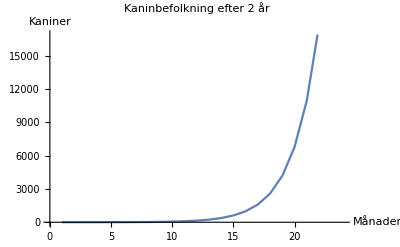

```mathematica
ListPlot[Table[Fibonacci[n],{n,24}],PlotLabel->"Kaninbefolkning efter 2 år",AxesLabel->{"Månader","Kaniner"},Joined->True]
```

### Undersök talföljden och diskutera tillväxtakten. Vilka begränsningar har modellen? Hur kan man förbättra modellen?

Vi ser att ekvationen blir fibonaccis talföljd. Tillväxttakten är enorm efter bara några få månader. Modellen är dock begränsad på det sättet att den inte tar hansyn till kaniner som dör av olika orsaker utan förutsätter en att alla kaniner som föds också förökar sig lika mycket.